## Lab Report 4 Francesco Vassalli

### Introduction

Op-amps are a useful active component in modern circuit design which can be used for feedback and voltage increase without significantly disturbing input signal.  We demonstrate the utility of op-amps with several non-inverting feedback loops.  A voltage follower provides utility for down-converting impedance and trivial baseline data. We predict the unity gain frequency and measure gain frequency dependence for each circuit. We also investigate the limitations of our op-amp.  Finally we demonstrate how an op-amp circuit can drive a load.

A_0 f_0=G_0 f_B=f_T

### Experiment

#### Voltage Follower

```mathematica
Grid[{{"Component","Measurment"},{"C1","10.37nF"},{"C2","10.25nF"},{"R","99.1Ω"},{"Rf","9.85kΩ"}},Frame->All]
```

Component | Measurment
C1 | 10.37nF
C2 | 10.25nF
R | 99.1Ω
Rf | 9.85kΩ

Measured values of components used in the lab.

```mathematica
Grid[{{"Unit Gain f_T","5 MHz"},{"DC voltage gain","25 V/mV || 106 dB"},{"V_out Max","12-13V"},{"I_max","10 mA"},{"Input R","10^12Ω"}},Frame->All]
```

Unit Gain f_T | 5 MHz
DC voltage gain | 25 V/mV || 106 dB
V_out Max | 12-13V
I_max | 10 mA
Input R | 10^12Ω

Manufacture specifications of the op-amp.

Schematic of the voltage follower with the pins of the op-amp labeled.

```mathematica
Grid[{{"Pin","Predicted","Measured"},{"2","0V","0.001V"},{"3","0V","0V"},{"4","-15V","-15V"},{"6","0V","0V"},{"7","15V","15V"}},Frame->All]
```

Pin | Predicted | Measured
2 | 0V | 0.001V
3 | 0V | 0V
4 | -15V | -15V
6 | 0V | 0V
7 | 15V | 15V

We investigate the behavior of the voltage follower by using the golden rules to predict the voltage at each pin.  Clearly the values agree.

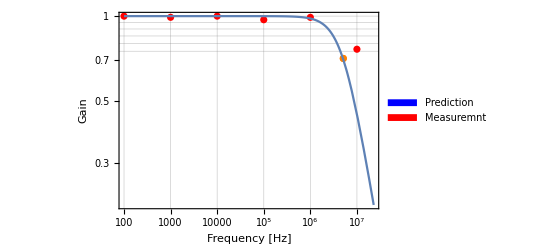

```mathematica
f=Table[10^(7-i),{i,0,5}];
vin={.8,1.02,1.03,1.03,1.04,1.04};
vout={.610,1.01,1,1.03,1.03,1.04};
gain=Table[Part[vout,i]/Part[vin,i],{i,6}];
main=ListPlot[Thread[{f,gain}],ScalingFunctions->{"Log","Log"},
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","Gain"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic,
PlotLegends->SwatchLegend[{Blue,Red},{"Prediction","Measuremnt"}]];
band=ListPlot[Thread[{{5.1*10^6},{.707}}],ScalingFunctions->{"Log","Log"},PlotStyle->Orange];
pfT=5*10^6;
R=Infinity;
Rf=0;
Subscript[pG, 0][Rf_,R_]:=1+Rf/R;
fB[Rf_,R_]:=pfT/(Subscript[pG, 0][Rf,R]);

pG[Rf_,R_,f_]:=Abs[(Subscript[pG, 0][Rf,R])/(1+ⅉ*f/fB[Rf,R])];
predictedFollower=LogLogPlot[pG[Rf,R,f],{f,100,10^8}];

Show[main,band,predictedFollower,PlotRange->All]
```

Gain of the voltage follower.  At low frequency G=1.  At high frequencies many of the components vary from ideal behavior and a negative gain is observed. The orange point is the measured f_B.

```mathematica
Grid[{{"","Predicted","Measured"},{"G_0","1","1"},{"f_B","5MHz","5.1MHz"},{"f_T","5MHz","5.1MHz"}},Frame->All]
```

| Predicted | Measured
G_0 | 1 | 1
f_B | 5MHz | 5.1MHz
f_T | 5MHz | 5.1MHz

The gain of the voltage shows G_0=1 which aggress with the golden rule.  The plot also demonstrates how the voltage follower has some similarity to a low pass filter.  However, the functional form of  a low pass filter would not explain the jump at extreme frequency. Using formula 1 our measurement of f_T agrees.

#### Negative Feedback Loop

Schematic of the closed feedback loop.

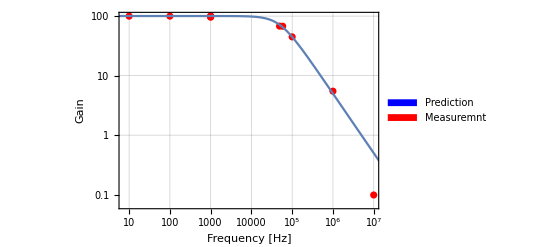

```mathematica
f={10^3,10^3,10^3,49*10^3,58.5*10^3,10^7,10^6,10^5,10^3,100,10};
vin={.103,.284,.287,.103,.105,.77,.104,.104,.104,.104,.104,.082};
vout={10.3,28.4,28,7,7.1,.076,.570,4.66,10,10.4,10.4,10.2};
gain=Table[Part[vout,i]/Part[vin,i],{i,Length[f]}];
main=ListPlot[Thread[{f,gain}],ScalingFunctions->{"Log","Log"},
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","Gain"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic,PlotLegends->SwatchLegend[{Blue,Red},{"Prediction","Measuremnt"}]];
R=99.1;
Rf=9.85*10^3;
predictedLoop=LogLogPlot[pG[Rf,R,f],{f,1,10^8}];
Show[main,predictedLoop]
```

Gain of the negative feedback loop.

```mathematica
Grid[{{"","Predicted","Measured"},{"G_0","1","1"},{"f_B","49.8kHz","58.5kHz"},{"f_T","5MHz","5.85MHz"}},Frame->All]
```

| Predicted | Measured
G_0 | 1 | 1
f_B | 49.8kHz | 58.5kHz
f_T | 5MHz | 5.85MHz

f_B was obtained by increasing frequency until there was a -3dB output. Equation 1 allows this measurement and the measurement of G_0 to make a measurement of f_T.

```mathematica
Grid[{{"+Vsat","28.4V"},{"-Vsat","28V"}},Frame->All]
```

+Vsat | 28.4V
-Vsat | 28V

Saturation voltage was measured by varying the input voltage in at 1kHz until the waveform was clipped.

Our measurements of gain roughly agree with prediction; however the measured f_B and f_T are significantly higher than predicted.  The saturation values cover more than the specified swing of the op-amp which leads me to believe that this is not a precise measurement.

R'_in=R_(op-amp in)(1+V_out/(V_in^+-V_in^-)*R/(R+R_f))

R'_out=(R_(op-amp out))/(1+V_out/(V_in^+-V_in^-)*R/(R+R_f))

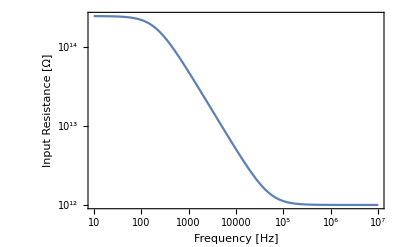

```mathematica
B[R_,Rf_]:=R/(R+Rf);
Subscript[A, 0]=25*10^3;
f0=pfT/Subscript[A, 0];
A[f_]:=Subscript[A, 0]/(1+ⅉ*f/f0)
Ri0=10^12;
Ri[R_,Rf_,f_]:=Ri0*(1+A[f]*B[R,Rf]);
pI=LogLogPlot[Abs[Ri[R,Rf,f]],{f,10,10^7},Frame->True,Axes->True,LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","Input Resistance [Ω]"},
FrameStyle->Thickness[.005]]
```

Predicted input resistance of the circuit using equation 2.

G_(resistor series input)=Z_Rs/(Z_Rs+Z_circuit)

Gain across a resistor placed in series with the input of the op-amp circuit.

The input impedance of the op-amp circuit is very high equation 4 predicts almost no voltage drop. We test this with a 996kΩ resistor and observe no change in the circuit output.

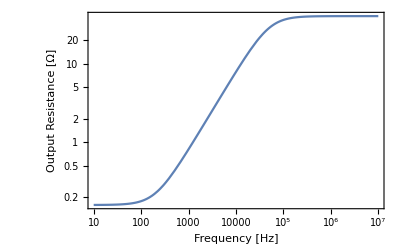

```mathematica
B[R_,Rf_]:=R/(R+Rf);
Subscript[A, 0]=25*10^3;
f0=pfT/Subscript[A, 0];
A[f_]:=Subscript[A, 0]/(1+ⅉ*f/f0)
Ro0=40;
Ro[R_,Rf_,f_]:=Ro0/(1+A[f]*B[R,Rf]);
pI=LogLogPlot[Abs[Ro[R,Rf,f]],{f,10,10^7},Frame->True,Axes->True,LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Frequency [Hz]","Output Resistance [Ω]"},
FrameStyle->Thickness[.005]]
```

Predicted output resistance of the circuit using equation 3.

```mathematica
Grid[{{"Load","Predicted V_out","Measured"},{"217Ω","9.52V","10.1V"},{"10Ω","3.47V","508mV"}},Frame->All]
```

Load | Predicted V_out | Measured
217Ω | 9.52V | 10.1V
10Ω | 3.47V | 508mV

These predictions are used to predict the voltage drop across a resistor when the circuit drives a load.

The 10Ω case disagrees with the prediction because the out is current limited.  We could modify the model to account for the maximum current output by the op-amp.

### Summary

We demonstrate several capabilities of an op-amp and models used to predict their performance. We find that simple circuit models agree up to about 10^7 Hz.  Our measurement of f_b in a negative feedback loop does not agree with prediction.  Predictions on voltage across a load agree until current limit.